# Computing Fourier Coefficients and Interpolation David Meretzky

```mathematica
(* 
given a function u evaluated at a set of points Subscript[x, 1]... Subscript[x, n] we compute the coefficients of the discrete fourier transform as follows:

Subscript[c, k] = ∑_(i=1)^n u(Subscript[x, i])* e^((2*π*ⅈ*k*i)/n)

We will calculate these coefficients using matrix multiplication.  The matrix for the discrete fourier transform is assembled as follows.  
Since Subscript[x, i] = 2*Pi/n * i =  Δx * i for a uniform partition, the k,ith entry of the  DFT matrix is given by
  
 e^((2*π*ⅈ*k*i)/n) 


*)
M = 8;
dftm = {};
(* from 0 to 7 *)
For[k =0, k ≤ M -1, ++k, 
(* make a new basis vector for each frequency *)
row = {};
For[i =0, i ≤ M-1, ++i,
 (* for a given frequency k, at each ith location compute the component of that basis vector *)
xi = 2*Pi/M * i;
AppendTo[row, E^(I*k*xi)];

];

AppendTo[dftm,row];
];
```

```mathematica
dftm = Simplify[dftm];
MatrixForm[dftm]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4))

```mathematica
(* normalizing the basis vectors*)
```

```mathematica
dftm = dftm/Sqrt[M];
```

```mathematica
(* Here we are just checking that it does indeed form a basis. *)
```

```mathematica
MatrixForm[Simplify[dftm].Simplify[dftm][[{1,8,7,6,5,4,3,2}]]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(*
 The signal given below is the binary ascii code for the character "b"   (this is the values of our function u at the positions xi = {0,1,2, ...,7})
*)
```

```mathematica
b = {0,1,1,0,0,0,1,0};
```

```mathematica
(* we compute the fourier coefficients with a simple matrix product *)
```

```mathematica
c = N[Simplify[dftm.b]]
```

{1.06066,0.25+0.25 ⅈ,-0.707107+0.353553 ⅈ,-0.25+0.25 ⅈ,0.353553,-0.25-0.25 ⅈ,-0.707107-0.353553 ⅈ,0.25-0.25 ⅈ}

```mathematica
(* using the coeffieicents we assemble the interpolation *)
```

```mathematica
M = 8;
interp = {};
Clear[x];
For[k =0, k ≤ M -1, ++k, 

f = 1/Sqrt[M]*(
Re[c[[k+1]]]*Cos[k* 2*Pi/M * x] +
Im[c[[k+1]]]*Sin[k* 2*Pi/M * x]
);
AppendTo[interp, f];

];
```

```mathematica
(* Some minor reformattting, slapping on x coordinates so they begin at 0 *)
```

```mathematica
b
```

{0,1,1,0,0,0,1,0}

```mathematica
(* now becomes*)
```

```mathematica
b = Partition[Riffle[Range[0,7],b],2]
```

{{0,0},{1,1},{2,1},{3,0},{4,0},{5,0},{6,1},{7,0}}

```mathematica
plist = {};
For[i =1, i ≤ M,i++,
AppendTo[plist, Show[{Plot[Total[interp[[1;;i]]],{x,0,8}, PlotRange -> {{0,8},{0,1.1}},AspectRatio->.3,ImageSize->Medium],ListPlot[l, Filling->Axis, AspectRatio->Full]}]];
AppendTo[plist,ListPlot[Re[c[[1;;i]]]^2 + Im[c[[1;;i]]]^2,AspectRatio->.3,Filling->Axis,PlotRange -> {{0,8},{0,2}},ImageSize->Medium]]

]
```

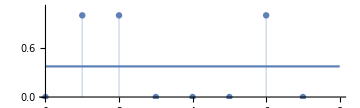
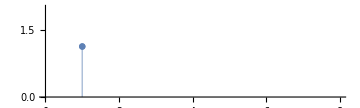
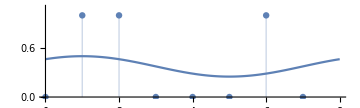
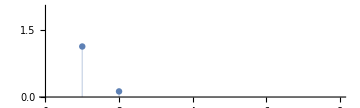
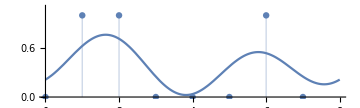
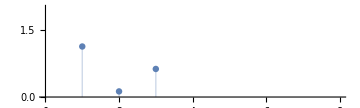
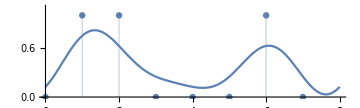
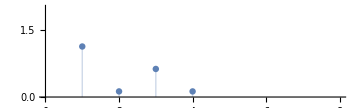

```mathematica
plist
```

# Applications to Data Transmission in Bandwidth Limited Media

```mathematica
(* The numbers in this example were taken from Tanenbaum's Computer Networks 5th edition *)
```

```mathematica
(*

Suppose we can transmit b bits/second. If we want to transmit 8 bits, using dimensional analysis we obtain the number of seconds as:

*)
```

```mathematica
8bits * sec/(b bits) = 8/b seconds
```

```mathematica
(*  if we have 1 bit per cycle, then the first harmonic (basis vector) has a frequency of  *)
```

```mathematica
b/8 Hz       (Hz =  cycles/second)
```

```mathematica
(* A voice grade telephone line has a bandwidth of 3000 Hz. Thus the highest harmonic number that we can pass through it is the dimensionless quantity computed below: *)
```

```mathematica
3000Hz/ (b/8)Hz  =  24000/b
```

```mathematica
(* Suppose I want to send 6000 bits per second then my 8 bits will look something like the third plot. *)
```

```mathematica
N[24000/6000]
```

4.

```mathematica
(* Below is the highest resolution, a sum of 8 basis vectors. *)
```

```mathematica
(* to obtain this resolution for our 8 bits, our bits per second rate through the phone line cannot go over 3000 *)
```

```mathematica
N[24000/8]
```

3000.